## 展开和变换

预备工作：

```mathematica
imgSize=300;
```

### 级数

#### 情形一

我们常常使用级数。那么级数如何形象的去理解呢？

举个例子说明，比如我们有一个这样的数列：

2,1/2,4/3,3/4,...,(n+(-1)^(n-1))/n,...

我们可以把这些数画在一个坐标系中。例如我们有这样一个数列：

```mathematica
exampleSeries1=(n+(-1)^(n-1))/n;
```

数列的前几项是：

```mathematica
Append[Table[exampleSeries1,{n,1,10}],"..."]
```

{2,1/2,4/3,3/4,6/5,5/6,8/7,7/8,10/9,9/10,...}

我们可以把各项在图上表示出来。其中

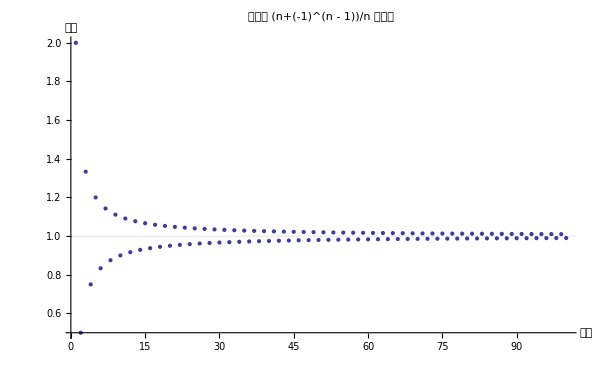
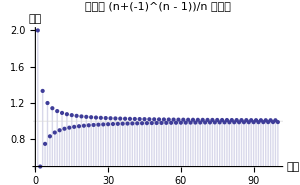
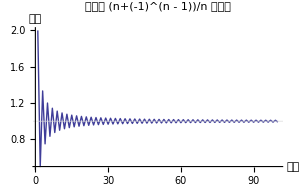

```mathematica
example1=Table[exampleSeries1,{n,1,100}];
Grid[{
{ListPlot[example1,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example1,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->imgSize]
ListPlot[example1,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 (n+(-1)^(n - 1))/n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],PlotRange->Full,ImageSize->imgSize]}
}]
```

从这个图中看到这个数列的极限通项大概是越来越接近 1 的。那么它的极限到底是不是 1 呢？

```mathematica
Limit[exampleSeries,n->Infinity]
```

1

确实是 1 。

#### 情形二

另一种情形是这样的。

```mathematica
exampleSeries2=2^-n;
```

```mathematica
Append[Table[exampleSeries2,{n,1,10}],"..."]
```

{1/2,1/4,1/8,1/16,1/32,1/64,1/128,1/256,1/512,1/1024,...}

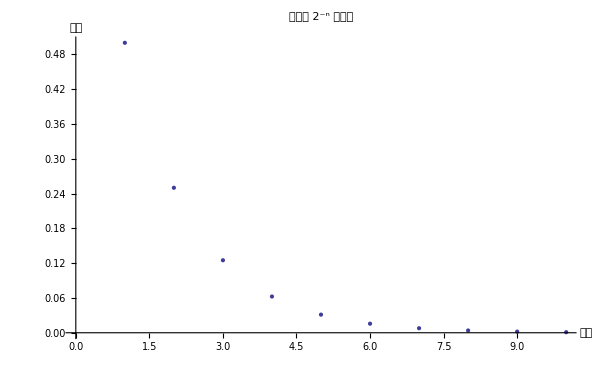
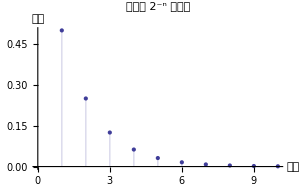
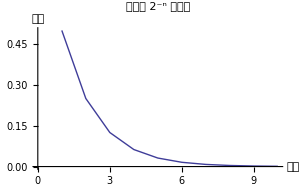

```mathematica
example2=Table[exampleSeries2,{n,1,10}];
Grid[{
{ListPlot[example2,GridLines->{{},{1}},PlotLabel->"通项为 2^-n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example2,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 2^-n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]
ListPlot[example2,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 2^-n 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

#### 情形三

```mathematica
exampleSeries3=Exp[-1/n];
```

```mathematica
Append[Table[exampleSeries3,{n,1,10}],"..."]
```

{1/ⅇ,1/(√ⅇ),1/ⅇ^(1/3),1/ⅇ^(1/4),1/ⅇ^(1/5),1/ⅇ^(1/6),1/ⅇ^(1/7),1/ⅇ^(1/8),1/ⅇ^(1/9),1/ⅇ^(1/10),...}

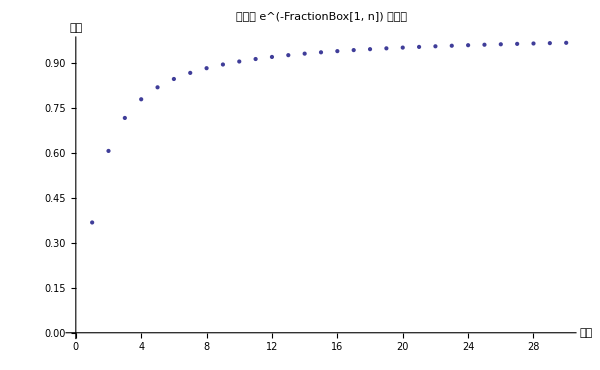
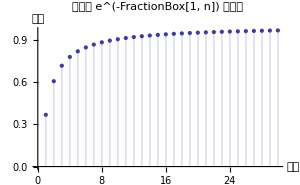
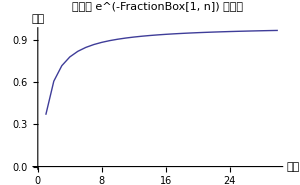

```mathematica
example3=Table[exampleSeries3,{n,1,30}];
Grid[{
{ListPlot[example3,GridLines->{{},{1}},PlotLabel->"通项为 e^(-FractionBox[1, n]) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example3,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 e^(-FractionBox[1, n]) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]
ListPlot[example3,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 e^(-FractionBox[1, n]) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

#### 情形四

```mathematica
exampleSeries4=Exp[-n Sin[1/n]];
```

```mathematica
Append[Table[exampleSeries4,{n,1,10}],"..."]
```

{ⅇ^(-Sin[1]),ⅇ^(-2 Sin[1/2]),ⅇ^(-3 Sin[1/3]),ⅇ^(-4 Sin[1/4]),ⅇ^(-5 Sin[1/5]),ⅇ^(-6 Sin[1/6]),ⅇ^(-7 Sin[1/7]),ⅇ^(-8 Sin[1/8]),ⅇ^(-9 Sin[1/9]),ⅇ^(-10 Sin[1/10]),...}

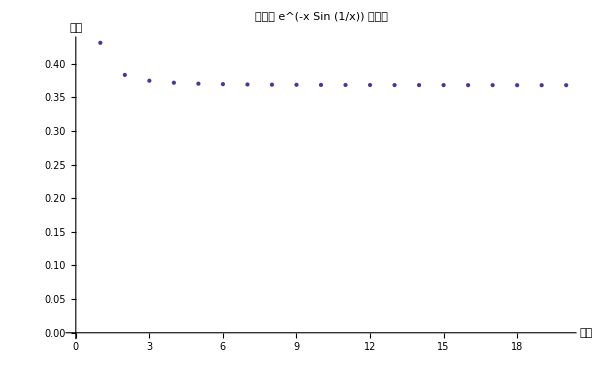
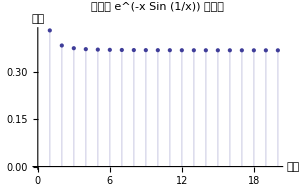
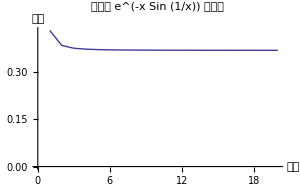

```mathematica
example4=Table[exampleSeries4,{n,1,20}];
Grid[{
{ListPlot[example4,GridLines->{{},{1}},PlotLabel->"通项为 e^(-x Sin (1/x)) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->2imgSize]},
{ListPlot[example4,Filling->Axis,GridLines->{{},{1}},PlotLabel->"通项为 e^(-x Sin (1/x)) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]
ListPlot[example4,Joined->True,GridLines->{{},{1}},PlotLabel->"通项为 e^(-x Sin (1/x)) 的数列",AxesLabel->{"项数","数列"},AxesStyle->Arrowheads[Automatic,Automatic],AxesOrigin->{0,0},PlotRange->Full,ImageSize->imgSize]}
}]
```

```mathematica
Limit[Exp[-n Sin[1/n]],n->Infinity]
```

1/ⅇ

有一点要很小心，即这个数量通项写出来虽然是一个递减的，然而这个通项所对应的连续自变量的函数却是个振荡的。

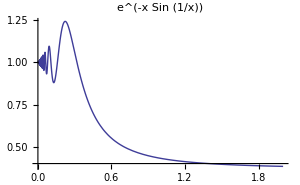

```mathematica
Plot[Exp[-x Sin[1/x]],{x,0,2},ImageSize->imgSize,PlotLabel->"e^(-x Sin (1/x))"]
```

这是一个有警示性的例子。有时候我们找了几个自变量，算了函数值，然后我们就武断的给出了函数是个单调性等性质，看看这个例子的情况，我们就知道有时候是必须很小心的。

#### 其他情形

当然还用其他的情形。比如函数一直保持在某值下方，但是却震荡着接近该值等等。还用趋于无穷的各种情况。